# SHAEAQ D1 Calculation

## Geometry Parameters

```mathematica
(* geometry *)
LtgtS0D = 1.155+0.3;
LS0DSQ1a=0.855;-0.3+0.8744+0.27462; (* m*)
LtgtSQ1a = LtgtS0D+LS0DSQ1a;
LSQ1eff =1.039;LSQ1= 0.940;
LSQ1bSQ2a=0.260;
LSQ2eff=0.539;LSQ2=0.440;
LSQ2bD1a=0.27438+0.481;
D1TurnAngle=32.7 Degree; (* rad *)
ρ0=4.4; (* mm *)
LD1= ρ0  D1TurnAngle;
LD1bS1=0.110+0.125;
LS1Hodo=0.125+0.160;
Brho=6.5269; (* T m *)
D1θ=13.65 Degree;
B0=Brho/ρ0; (* T *)
aQ1x=0.17;aQ1y=0.17; B0Q1=7.739;
aQ2x=0.17;aQ2y=0.17;B0Q2=6.000;
```

```mathematica
LtgtS1=LtgtSQ1a+LSQ1+LSQ1bSQ2a+LSQ2+LSQ2bD1a+LD1+LD1bS1/Cos[13.5 Degree]
LS0DS1 = LtgtS1-LtgtS0D
```

7.45824

6.00324

## 1st Order transport Matrix

```mathematica
(*Drift*)
R0[L_]:={
{1,L,0,0,0,0},
{0,1,0,0,0,0},
{0,0,1,L,0,0},
{0,0,0,1,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}
};
(* Dipole , kx^2= (1-n)h^2, ky^2= n h^2, n is the gradient of By along x , usually 0 ; direction of h is oppsite to beam coordinate*)
R1[kx_,ky_,h_,L_]:={
{Cos[kx L], 1/kx Sin[kx L], 0, 0, 0, h/kx^2(1-Cos[kx L])},
{-kx Sin[kx L], Cos[kx L], 0, 0, 0, h/kx Sin[kx L]},
{0,0, Cos[ky L],If[ky==0,L, 1/ky Sin[ky L]], 0, 0},
{0,0,-ky Sin[ky L], Cos[ky L], 0, 0},
{h/kx Sin[kx L], h/kx^2(1-Cos[kx L]), 0,0, 1, h^2/kx^3(kx L - Sin[kx L])},
{0,0,0,0,0,1}
};
(* Quadrupole, kq^2=Gradiance[B0] 1/Brho , Brho = P0/e*) 
R2[kq_,L_]:={
{Cos[kq L], 1/kq Sin[kq L], 0, 0, 0,0},
{-kq Sin[kq L], Cos[kq L],0, 0, 0,0},
{0, 0, Cosh[kq L],If[kq==0,L, 1/kq Sinh[kq L]], 0,0},
{0,0, kq Sinh[kq L], Cosh[kq L],0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}};
```

```mathematica
(* Right-hand Rotation about Y-axis*)
```

## 1 st order Calculation

```mathematica
(* Transport matrix 1st order *)
SDQ1=Re[R0[LSQ1bSQ2a].R2[√(-B0Q1/(LSQ1eff  Brho)),LSQ1eff].R0[LtgtSQ1a]];SDQ1//MatrixForm
SDQ2=Re[R0[LSQ2bD1a].R2[√(B0Q2/(LSQ2eff Brho)),LSQ2eff]];SDQ2//MatrixForm
SDQ=SDQ2.SDQ1;SDQ//MatrixForm
D1=R0[LD1bS1].R1[-1/ρ0, 0,- 1/ρ0, LD1];D1//MatrixForm
M=D1.SDQ;M//MatrixForm
```

(2.05747 | 6.4559 | 0. | 0. | 0. | 0.
1.44461 | 5.01891 | 0. | 0. | 0. | 0.
0. | 0. | 0.195949 | 1.4067 | 0. | 0.
0. | 0. | -0.956816 | -1.76552 | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

(0.123858 | 1.07142 | 0. | 0. | 0. | 0.
-0.845217 | 0.762318 | 0. | 0. | 0. | 0.
0. | 0. | 2.01133 | 1.535 | 0. | 0.
0. | 0. | 0.99709 | 1.25814 | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

(1.80261 | 6.17697 | 0. | 0. | 0. | 0.
-0.637753 | -1.63062 | 0. | 0. | 0. | 0.
0. | 0. | -1.0746 | 0.119245 | 0. | 0.
0. | 0. | -1.00843 | -0.818677 | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

(0.812657 | 2.57481 | 0. | 0. | 0. | -0.824309
-0.122782 | 0.841511 | 0. | 0. | 0. | -0.54024
0. | 0. | 1. | 2.74618 | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
-0.54024 | -0.697353 | 0. | 0. | 1. | 0.134122
0. | 0. | 0. | 0. | 0. | 1.)

(-0.177189 | 0.821209 | 0. | 0. | 0. | -0.824309
-0.758005 | -2.13061 | 0. | 0. | 0. | -0.54024
0. | 0. | -3.84394 | -2.12899 | 0. | 0.
0. | 0. | -1.00843 | -0.818677 | 0. | 0.
-0.529106 | -2.19993 | 0. | 0. | 1. | 0.134122
0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
M.{x,a,y,b,0,δ}//MatrixForm
```

(0.+0.821209 a-0.177189 x+0.824309 δ
0.-2.13061 a-0.758005 x+0.54024 δ
0.-2.12899 b-3.84394 y
0.-0.818677 b-1.00843 y
0.+2.19993 a+0.529106 x+0.134122 δ
0.+1. δ)

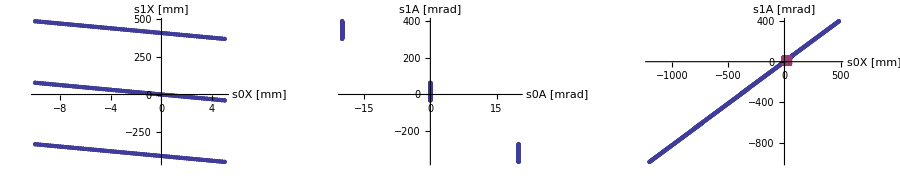

```mathematica
GraphicsGrid[{{
ListPlot[Flatten[Table[Join[{x },(SDQ.{x,a,0,0,0,δ})[[{1}]]]1000,{a,-0.02,0.02,0.02},{x,-0.01,0.005,0.0002},{δ,-0.01,0.01,0.01}],2],AxesLabel->{"s0X [mm]","s1X [mm]"}],
ListPlot[Flatten[Table[Join[{a},(SDQ.{x,a,0,0,0,δ})[[{2}]]]1000,{a,-0.02,0.02,0.02},{x,-0.01,0.005,0.0002},{δ,-0.01,0.01,0.01}],2],AxesLabel->{"s0A [mrad]","s1A [mrad]"}],
ListPlot[
{Flatten[Table[(SDQ.{x,a,0,0,0,δ})[[{1,2}]]1000,{a,-0.02,0.04,0.02},{x,-0.01,0.05,0.001},{δ,-0.01,0.01,0.01}],2],
Flatten[Table[{x,a}1000,{a,-0.02,0.04,0.02},{x,-0.01,0.05,0.001},{δ,-0.01,0.01,0.01}],2]
},AxesLabel->{"s0X [mm]","s1A [mrad]"}]
}},ImageSize->900]
```

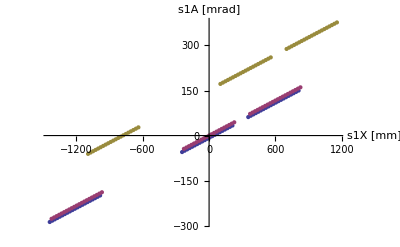

```mathematica
ListPlot[{
Flatten[Table[(M.{x,a,0,0,0,0.02})[[{1,2}]]1000,{a,{-0.01,0.0, 0.02}},{x,-0.01,0.01,0.001}],1],
Flatten[Table[(M.{x,a,0,0,0,0})[[{1,2}]]1000,{a,{-0.01,0.0, 0.02}},{x,-0.01,0.01,0.001}],1],
Flatten[Table[(M.{x,a,0,0,0,-0.4})[[{1,2}]]1000,{a,{-0.01,0.0, 0.02}},{x,-0.01,0.01,0.001}],1]
},AxesLabel->{"s1X [mm]","s1A [mrad]"}]
```

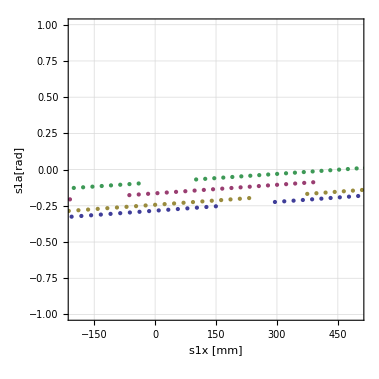

```mathematica
ListPlot[{
Flatten[Table[kkk=(M.{x,a,0,0,0,0.1})[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.01}},{x,-0.01,0.01,0.001}],1],
Flatten[Table[kkk=(M.{x,a,0,0,0,-0.2})[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.01}},{x,-0.01,0.01,0.001}],1],
Flatten[Table[kkk=(M.{x,a,0,0,0,0})[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.01}},{x,-0.01,0.01,0.001}],1],
Flatten[Table[kkk=(M.{x,a,0,0,0,-0.4})[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.01}},{x,-0.01,0.01,0.001}],1]
},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["s1x [mm]",14],Style["s1a[rad]",14]},PlotRange->{{-200,500},{-1,1}},AspectRatio->1]
```

```mathematica
kkk=M.{x,a,0,0,0,δ};
kkk//MatrixForm
Series[{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ]),  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])}, {x,0,1},{a,0,1},{δ,0,1}]
```

(0.+14.8808 a+6.7095 x-0.824309 δ
0.+4.19181 a+1.82282 x-0.54024 δ
0.
0.
0.-4.58385 a-2.12218 x+0.134122 δ
0.+1. δ)

{((-0.848268 δ+O[δ]^2)+(15.3133+2.87258 δ+O[δ]^2) a+O[a]^2)+((6.90452+1.28136 δ+O[δ]^2)+(-13.8074-4.38748 δ+O[δ]^2) a+O[a]^2) x+O[x]^2,((-0.242849-0.572101 δ+O[δ]^2)+(4.43902+1.16477 δ+O[δ]^2) a+O[a]^2)+((1.93032+0.506504 δ+O[δ]^2)+(-3.93005-1.54683 δ+O[δ]^2) a+O[a]^2) x+O[x]^2}

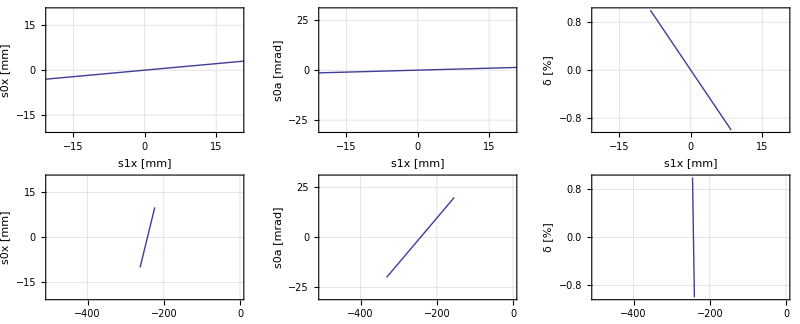

```mathematica
M1={{6.90, 15.31, -0.8483},{1.930,4.439,-0.2428},{0,0,1}};
C1={0,-0.243,0};
GraphicsGrid[{{
ListPlot[Table[{(M1.{x,0,0}+C1)[[1]]1000,x 1000},{x,-0.01,0.01,0.001}],PlotRange->{{-20,20},{-20,20}},Joined->True,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["s1x [mm]",14],Style[ "s0x [mm]",14]}],
ListPlot[Table[{(M1.{0,a,0}+C1)[[1]]1000,a 1000},{a,-0.02,0.02,0.0001}],PlotRange->{{-20,20},{-30,30}},Joined->True,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["s1x [mm]",14],Style[ "s0a [mrad]",14]}],
ListPlot[Table[{(M1.{0,0,δ}+C1)[[1]]1000,δ 100},{δ,-0.01,0.01,0.001}],PlotRange->{{-20,20},{-1,1}},Joined->True,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["s1x [mm]",14],Style[ "δ [%]",14]}]
},{
ListPlot[Table[{(M1.{x,0,0}+C1)[[2]]1000,x 1000},{x,-0.01,0.01,0.001}],PlotRange->{{-500,0},{-20,20}},Joined->True,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["s1a[mrad]",14],Style[ "s0x [mm]",14]}],
ListPlot[Table[{(M1.{0,a,0}+C1)[[2]]1000,a 1000},{a,-0.02,0.02,0.0001}],PlotRange->{{-500,0},{-30,30}},Joined->True,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["s1a [mrad]",14],Style[ "s0a [mrad]",14]}],
ListPlot[Table[{(M1.{0,0,δ}+C1)[[2]]1000,δ 100},{δ,-0.01,0.01,0.001}],PlotRange->{{-500,0},{-1,1}},Joined->True,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["s1a [mrad]",14],Style[ "δ [%]",14]}]
}
}
,ImageSize->800]
```

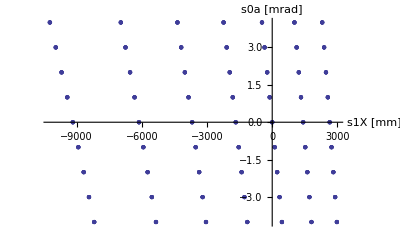

```mathematica
ListPlot[Flatten[Table[kkk=(M.{x,a,0,0,0,δ})[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,x 1000},{a,-0.01,0.020,0.005},{x,-0.004,0.004,0.001},{δ,-0.002,0.002,0.001}],2],AxesLabel->{"s1X [mm]","s0a [mrad]"}]
```

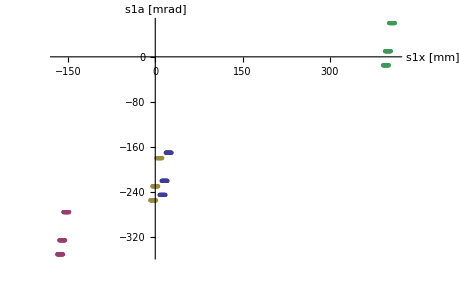

```mathematica
ExpM={
{0.5, 0.35, -16},
{0, 2.5, -9.6},
{0,0,1}};
ListPlot[{
Flatten[Table[(ExpM.{x,a,-1})[[{1,2}]]+{0,-230},{a,{-10,0,20}},{x,-10,10,1}],1],
Flatten[Table[(ExpM.{x,a,10})[[{1,2}]]+{0,-230},{a,{-10,0,20}},{x,-10,10,1}],1],
Flatten[Table[(ExpM.{x,a,0})[[{1,2}]]+{0,-230},{a,{-10,0,20}},{x,-10,10,1}],1],
Flatten[Table[(ExpM.{x,a,-25})[[{1,2}]]+{0,-230},{a,{-10,0,20}},{x,-10,10,1}],1]
},AxesLabel->{"s1x [mm]","s1a [mrad]"}]
```

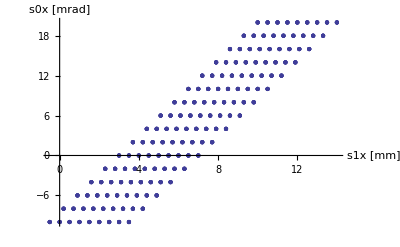

```mathematica
ExpM={
{0.5, 0.35, -16},
{0, 2.5, -8},
{0,0,1}};ListPlot[{
Flatten[Table[kkk=(ExpM.{x,a,-1})+{-11,-230,0};{kkk[[1]], a},{a,-10,20,2},{x,-4,4,1},{δ,-0.2,0.2,0.1}],2]
},AxesLabel->{"s1x [mm]","s0x [mrad]"}]
```

## 2 nd order transport Matrix Simple

```mathematica
(* Dipole Entrance and exist *)
R1ends[β_,R_,h_,ψ_]:={
{1,0, 0, 0, 0,0},
{h Tan[β], 1, 0, 0, 0,0},
{0,0,1,0,0,0},
{0,0,-h Tan[β-ψ],1,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,1}
};
T1entrance[β_,R_,h_,n_,ψ_]:={
{{-h/2 Tan[β]^2,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,h/2 Sec[β]^2,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{h/(2R)Sec[β]^2-n h^2 Tan[β],h Tan[β]^2, 0, 0, 0,-h Tan[β]},
{0,0,0, 0, 0,0},
{0, 0,h^2(n+1/2+Tan[β]^2)Tan[β]-h/(2R)Sec[β]^3,-h Tan[β]^2, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, h Tan[β]^2, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, -h/R Sec[β]^2+2 h^2 n Tan[β], -h Tan[β]^2, 0,0},
{0,0,-h Sec[β]^2, 0, 0,0},
{0, 0,0,0, 0,h Tan[β]-h ψ Sec[β-ψ]^2},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}}
}
T1exit[β_,R_,h_,n_,ψ_]:={
{{h/2 Tan[β]^2,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,-h/2 Sec[β]^2,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{h/(2R)Sec[β]^2- h^2(n+1/2 Tan[β]^2) Tan[β],-h Tan[β]^2, 0, 0, 0,-h Tan[β]},
{0,0,0, 0, 0,0},
{0, 0,h^2(n-1/2 Tan[β]^2)Tan[β]-h/(2R)Sec[β]^3,h Tan[β]^2, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, -h Tan[β]^2, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, -h/R Sec[β]^2+h^2 (2n+Sec[β]^2) Tan[β], h Tan[β]^2, 0,0},
{0,0,h Sec[β]^2, 0, 0,0},
{0, 0,0,0, 0,h Tan[β]-h ψ Sec[β-ψ]^2},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}}
}
(* Quadrupole *)
T2[kq_,L_]:={
{{0,0, 0, 0, 0,1/2 kq L Sin[kq L]},
{0,0,0, 0, 0,1/(2 kq) Sin[kq L]-L/2 Cos[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,kq/2(kq L Cos[kq L]+Sin[kq L])},
{0,0,0, 0, 0,1/2 kq L Sin[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,-1/2 kq L Sinh[kq L]},
{0,0,0, 0, 0,1/2(1/kq Sinh[kq L]-L Cosh[kq L])},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,-kq/2(kq L Cosh[kq L]+Sinh[kq L])},
{0,0,0, 0, 0,-kq/2 L Sinh[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}}
}
```

### Calculation

```mathematica
SDQ1=Re[R2[√(-B0Q1/(aQ1x Brho)),LSQ1eff].R0[LtgtSQ1a]];
SDQ2=Re[R0[LSQ2bD1a].R2[√(B0Q2/(aQ2x Brho)),LSQ1eff].R0[LSQ1bSQ2a]];
SDQ=SDQ2.SDQ1;
D1=R0[LD1bS1].R1[-1/ρ0, 0,- 1/ρ0, LD1];
M=D1.SDQ;M//MatrixForm
```

(-3.83537 | -6.5775 | 0. | 0. | 0. | -0.824309
-1.62289 | -3.04392 | 0. | 0. | 0. | -0.54024
0. | 0. | -7.8331 | 0.503668 | 0. | 0.
0. | 0. | -1.86716 | -0.00760481 | 0. | 0.
0.734257 | 1.0443 | 0. | 0. | 1. | 0.134122
0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
SDQ1G[x_,a_,y_,b_,0,δ_]:=SDQ1.{x,a,y,b,0,δ}+Re[T2[√(-B0Q1/(aQ1x Brho)),LSQ1eff]].{x,a,y,b,0,δ}.{x,a,y,b,0,δ}
SDQG[x_,a_,y_,b_,0,δ_]:=R0[LSQ2bD1a].(Re[R2[√(B0Q2/(aQ2x Brho)),LSQ1eff]].R0[LSQ1bSQ2a].SDQ1G[x,a,y,b,0,δ]+Re[T2[√(B0Q2/(aQ2x Brho)),LSQ2eff]].(R0[LSQ1bSQ2a].SDQ1G[x,a,y,b,0,δ]).(R0[LSQ1bSQ2a].SDQ1G[x,a,y,b,0,δ]))
D1aG[x_,a_,y_,b_,0,δ_]:=Re[R1ends[-13.7 Degree,∞,-1/ρ0,0]].SDQG[x,a,y,b,0,δ]+Re[T1entrance[-13.7Degree, ∞,-1/ρ0,0,0]].SDQG[x,a,y,b,0,δ].SDQG[x,a,y,b,0,δ]
D1mG[x_,a_,y_,b_,0,δ_]:=Re[R1[-1/ρ0, 0,- 1/ρ0, LD1]].D1aG[x,a,y,b,0,δ]
MG[x_,a_,y_,b_,0,δ_]:=Re[R1ends[-13.7 Degree,∞,-1/ρ0,0]].D1mG[x,a,y,b,0,δ]+Re[T1exit[-13.7Degree, ∞,-1/ρ0,0,0]].D1mG[x,a,y,b,0,δ].D1mG[x,a,y,b,0,δ]
```

```mathematica
kkk=MG[x,a,0,0,0,δ];
kkk//MatrixForm
Series[{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ]),  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])}, {x,0,1},{a,0,1},{δ,0,1}]
```

(«1»)

{((-0.717621 δ+O[δ]^2)+(-9.67565+16.0056 δ+O[δ]^2) a+O[a]^2)+((-3.42548+5.32652 δ+O[δ]^2)+(-8.56292+25.2152 δ+O[δ]^2) a+O[a]^2) x+O[x]^2,((-0.242849-0.613016 δ+O[δ]^2)+(-5.59151+4.69203 δ+O[δ]^2) a+O[a]^2)+((-1.86694+2.27635 δ+O[δ]^2)+(-4.1722+9.21139 δ+O[δ]^2) a+O[a]^2) x+O[x]^2}

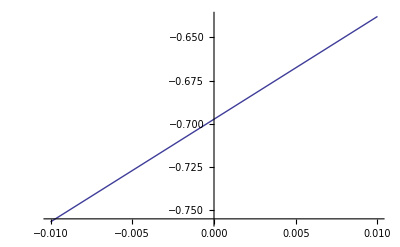

```mathematica
Plot[((MG[x,0,0,0,0,δ][[1]]//Simplify)[[2]])/δ,{x,-0.01,0.01}]
```

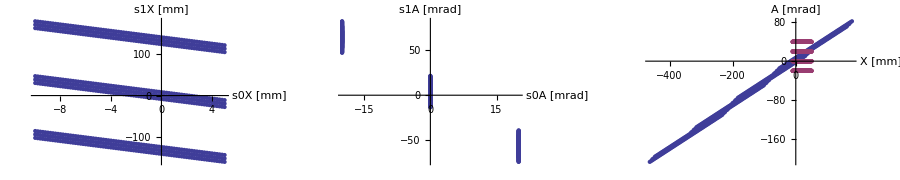

```mathematica
GraphicsGrid[{{
ListPlot[Flatten[Table[Join[{x },(M.{x,a,0,0,0,δ})[[{1}]]]1000,{a,-0.02,0.02,0.02},{x,-0.01,0.005,0.0002},{δ,-0.01,0.01,0.01}],2],AxesLabel->{"s0X [mm]","s1X [mm]"}],
ListPlot[Flatten[Table[Join[{a},(M.{x,a,0,0,0,δ})[[{2}]]]1000,{a,-0.02,0.02,0.02},{x,-0.01,0.005,0.0002},{δ,-0.01,0.01,0.01}],2],AxesLabel->{"s0A [mrad]","s1A [mrad]"}],
ListPlot[
{Flatten[Table[(M.{x,a,0,0,0,δ})[[{1,2}]]1000,{a,-0.02,0.04,0.02},{x,-0.01,0.05,0.001},{δ,-0.01,0.01,0.01}],2],
Flatten[Table[{x,a}1000,{a,-0.02,0.04,0.02},{x,-0.01,0.05,0.001},{δ,-0.01,0.01,0.01}],2]
},AxesLabel->{"X [mm]","A [mrad]"}]
}},ImageSize->900]
```

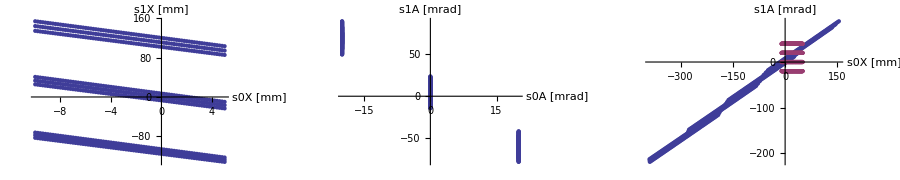

```mathematica
GraphicsGrid[{{
ListPlot[Flatten[Table[Join[{x },(MG[x,a,0,0,0,δ])[[{1}]]]1000,{a,-0.02,0.02,0.02},{x,-0.01,0.005,0.0002},{δ,-0.01,0.01,0.01}],2],AxesLabel->{"s0X [mm]","s1X [mm]"}],
ListPlot[Flatten[Table[Join[{a},(MG[x,a,0,0,0,δ])[[{2}]]]1000,{a,-0.02,0.02,0.02},{x,-0.01,0.005,0.0002},{δ,-0.01,0.01,0.01}],2],AxesLabel->{"s0A [mrad]","s1A [mrad]"}],
ListPlot[
{Flatten[Table[(MG[x,a,0,0,0,δ])[[{1,2}]]1000,{a,-0.02,0.04,0.02},{x,-0.01,0.05,0.001},{δ,-0.01,0.01,0.01}],2],
Flatten[Table[{x,a}1000,{a,-0.02,0.04,0.02},{x,-0.01,0.05,0.001},{δ,-0.01,0.01,0.01}],2]
},AxesLabel->{"s0X [mm]","s1A [mrad]"}]
}},ImageSize->900]
```

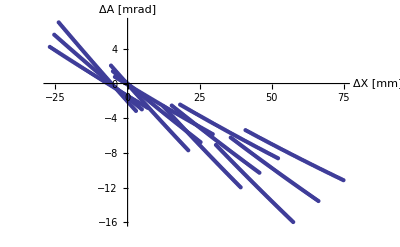

```mathematica
ListPlot[
{Flatten[Table[(MG[x,a,0,0,0,δ])[[{1,2}]]1000-(M.{x,a,0,0,0,δ})[[{1,2}]]1000,{a,-0.02,0.04,0.02},{x,-0.01,0.05,0.001},{δ,-0.01,0.01,0.01}],2]
},AxesLabel->{"ΔX [mm]","ΔA [mrad]"}]
```

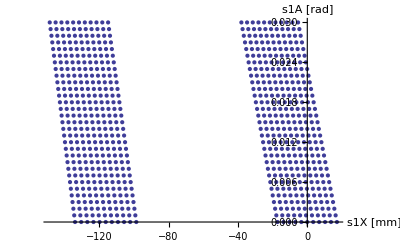

```mathematica
ListPlot[{
Flatten[Table[kkk=(MG[x,a,0,0,0,δ])[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,δ},{a,{0.0, 0.02}},{x,-0.005,0.005,0.001},{δ,-0.0,0.03,0.001}],2]
},AxesLabel->{"s1X [mm]","s1A [rad]"}]
```

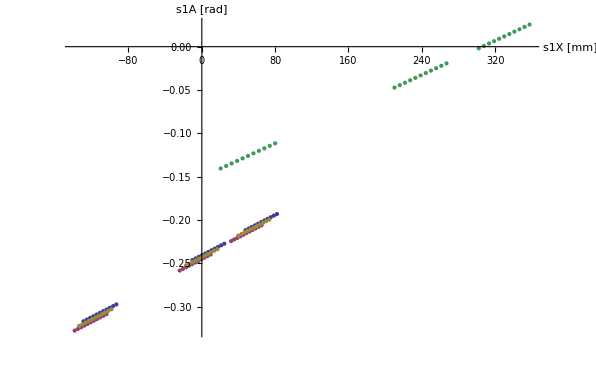

```mathematica
ListPlot[{
Flatten[Table[kkk=(MG[x,a,0,0,0,-0.01])[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.02}},{x,-0.005,0.005,0.001}],1],
Flatten[Table[kkk=(MG[x,a,0,0,0,0.01])[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.02}},{x,-0.005,0.005,0.001}],1],
Flatten[Table[kkk=(MG[x,a,0,0,0,0])[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.02}},{x,-0.005,0.005,0.001}],1],
Flatten[Table[kkk=(MG[x,a,0,0,0,-0.35])[[{1,2}]];{kkk[[1]]/(Cos[D1θ]+kkk[[2]]Sin[D1θ])1000,  (kkk[[2]]-Tan[D1θ])/(1+kkk[[2]]Tan[D1θ])},{a,{-0.01,0.0, 0.02}},{x,-0.005,0.005,0.001}],1]
},AxesLabel->{"s1X [mm]","s1A [rad]"}]
```

## 2nd order transport Matrix Complete

```mathematica
(* kx^2= (1-n)h^2, ky^2= n h^2, h= 1/ρ0 *)
cos[k_,L_]:=Cos[k L];
sin[k_,L_]:=If[k==0,L, 1/k Sin[k L]];
dx[kx_,h_,L_]:=h/kx^2(1-Cos[kx L]);
I10[kx_,ky_,h_,L_]:=dx[kx,h,L]/h
I11[kx_,ky_,h_,L_]:=1/2 L sin[kx,L]
I12[kx_,ky_,h_,L_]:=1/(2 kx^2)(sin[kx,L]-L cos[kx,L])
I16[kx_,ky_,h_,L_]:=h/kx^2(dx[kx,h,L]/h-L/2 sin[kx,L])
I111[kx_,ky_,h_,L_]:=1/3(sin[kx,L]^2+dx[kx,h,L]/h)
I112[kx_,ky_,h_,L_]:=1/3 sin[kx,L] dx[kx,h,L]/h
I116[kx_,ky_,h_,L_]:=h/kx^2(L/2 sin[kx,L]-1/3(sin[kx,L]^2+dx[kx,h,L]/h))
I122[kx_,ky_,h_,L_]:=1/(3 kx^2)(2 dx[kx,h,L]/h-sin[kx,L]^2)
I126[kx_,ky_,h_,L_]:=h/(6 kx^4)(sin[kx,L]+2sin[kx,L]cos[kx,L]-3L cos[kx,L])
I166[kx_,ky_,h_,L_]:=h^2/kx^4(4/3 dx[kx,h,L]/h+1/3 sin[kx,L]^2-L sin[kx,L])
I133[kx_,ky_,h_,L_]:=dx[kx,h,L]/h-ky^2/(kx^2-4 ky^2)(sin[ky,L]^2-2 dx[kx,h,L]/h)
I134[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(sin[ky,L]cos[ky,L]-sin[kx,L])
I144[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(sin[ky,L]^2-2 dx[kx,h,L]/h)
I20[kx_,ky_,h_,L_]:=sin[kx,L]
I21[kx_,ky_,h_,L_]:=1/2(sin[kx,L]+L cos[kx,L])
I22[kx_,ky_,h_,L_]:=1/2 L sin[kx,L]
I26[kx_,ky_,h_,L_]:=h/(2 kx^2)(sin[kx,L]-L cos[kx,L])
I211[kx_,ky_,h_,L_]:=sin[kx,L]/3(1+2 cos[kx,L])
I212[kx_,ky_,h_,L_]:=1/3(2 sin[kx,L]^2-dx[kx,h,L]/h)
I216[kx_,ky_,h_,L_]:=h/kx^2(L cos[kx,L]/2+sin[kx,L]/6-(2 sin[kx,L]cos[kx,L])/3)
I222[kx_,ky_,h_,L_]:=2/3 sin[kx,L] dx[kx,h,L]/h
I226[kx_,ky_,h_,L_]:=h/kx^2(1/2 L sin[kx,L]-2/3 sin[kx,L]^2+1/3 dx[kx,h,L]/h)
I266[kx_,ky_,h_,L_]:=h^2/kx^4(1/3 sin[kx,L]+2/3 sin[kx,L]cos[kx,L]-L cos[kx,L])
I233[kx_,ky_,h_,L_]:=sin[kx,L]-(2 kx^2)/(kx^2-4 ky^2)(sin[ky,L]cos[ky,L]-sin[kx,L])
I234[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(kx^2 dx[kx,h,L]/h-2 ky^2 sin[ky,L]^2) 
I244[kx_,ky_,h_,L_]:=2/(kx^2-4 ky^2)(sin[ky,L]cos[ky,L]-sin[kx,L])
I30[kx_,ky_,h_,L_]:=(1-cos[ky,L])/ky^2
I33[kx_,ky_,h_,L_]:=1/2 L sin[ky,L]
I34[kx_,ky_,h_,L_]:=1/(2 ky^2)(sin[ky,L]-L cos[ky,L])
I313[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(kx^2 cos[ky,L] dx[kx,h,L]/h-2 ky^2 sin[kx,L]sin[ky,L])
I314[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(2sin[kx,L]cos[ky,L]-sin[ky,L](1+cos[kx,L]))
I323[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(2 ky^2/kx^2 sin[ky,L](1+cos[kx,L])-sin[kx,L]cos[ky,L])+sin[ky,L]/kx^2
I324[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(2cos[ky,L] dx[kx,h,L]/h-sin[kx,L]sin[ky,L])
I336[kx_,ky_,h_,L_]:=h/kx^2(L/2 sin[ky,L]-1/(kx^2-4 ky^2)(cos[ky,L](1-cos[kx,L])-2 ky^2 sin[kx,L]sin[ky,L]))
I346[kx_,ky_,h_,L_]:=h/kx^2(1/ky^2(sin[ky,L]-L cos[ky,L])-1/(kx^2-4 ky^2)(2sin[kx,L]cos[ky,L]-sin[ky,L](1+cos[kx,L])))
I40[kx_,ky_,h_,L_]:=sin[ky,L]
I43[kx_,ky_,h_,L_]:=1/2(sin[ky,L]+L cos[ky,L])
I44[kx_,ky_,h_,L_]:=1/2 L sin[ky,L]
I413[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)((kx^2-2 ky^2)sin[kx,L]cos[ky,L]-ky^2 sin[ky,L](1+cos[kx,L]))
I414[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)((kx^2-2 ky^2)sin[kx,L]sin[ky,L]-cos[ky,L](1-cos[kx,L]))
I423[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(2 ky^2/kx^2 cos[ky,L](1+cos[kx,L])-cos[kx,L]cos[ky,L]-ky^2 sin[kx,L]sin[ky,L])+cos[ky,L]/kx^2
I424[kx_,ky_,h_,L_]:=1/(kx^2-4 ky^2)(cos[ky,L]sin[kx,L]-cos[kx,L]sin[ky,L]-2 ky^2 sin[ky,L] dx[kx,h,L]/h)
I436[kx_,ky_,h_,L_]:=h/kx^2(L/2 cos[ky,L]+sin[ky,L]/2+1/(kx^2-4 ky^2)(ky^2 sin[ky,L](1+cos[kx,L])-(kx^2-2 ky^2)sin[kx,L]cos[ky,L]))
I446[kx_,ky_,h_,L_]:=h/kx^2(L/2 sin[ky,L]-1/(kx^2-4 ky^2)((kx^2-2 ky^2)sin[kx,L]cos[ky,L]-cos[ky,L](1-cos[kx,L])))
TG[n_,β_,kx_,ky_,h_,L_]:={
{{(2n-1-β)h^3 I111[kx,ky,h,L]+1/2 kx^4 h I122[kx,ky,h,L],h sin[kx,L]+2(2n-1-β)h^3 I112[kx,ky,h,L]-kx^2 I112[kx,ky,h,L], 0, 0, 0,(2-n)h^2 I11[kx,ky,h,L]+(2n-1-β)h^3 I116[kx,ky,h,L]-kx^2 h^2 I122[kx,ky,h,L]},
{0,(2n-1-β)h^3 I122[kx,ky,h,L]+1/2 h I111[kx,ky,h,L],0, 0, 0,(2-n)h^2 I12[kx,ky,h,L]+(2n-1-β)h^3 I126[kx,ky,h,L]+h^2 I112[kx,ky,h,L]},
{0, 0,β h^3 I133[kx,ky,h,L]-1/2 ky^2 h I10[kx,ky,h,L],2 β h^3 I134[kx,ky,h,L], 0,0},
{0,0, 0,β h^3 I144[kx,ky,h,L]-1/2 h I10[kx,ky,h,L],0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,-h I10[kx,ky,h,L]+(2-n)h^2 I16[kx,ky,h,L]+(2n-1-β)h^3 I166[kx,ky,h,L]+1/2 h^3 I122[kx,ky,h,L]}},
{{(2n-1-β)h^3 I211[kx,ky,h,L]+1/2 kx^4 h I222[kx,ky,h,L]+h kx^2 cos[kx,L]sin[kx,L],h cos[kx,L]+2(2n-1-β)h^3 I212[kx,ky,h,L]- kx^2 I212[kx,ky,h,L]-h(cos[kx,L]^2-kx^2 sin[kx,L]), 0, 0, 0,(2-n)h^2 I21[kx,ky,h,L]+(2n-1-β)h^3 I216[kx,ky,h,L]-kx^2 h^2 I222[kx,ky,h,L]-h (cos[kx,L]sin[kx,L]-kx^2 sin[kx,L]dx[kx,h,L])},
{0,(2n-1-β)h^3 I222[kx,ky,h,L]+1/2 h I211[kx,ky,h,L]-h sin[kx,L]cos[kx,L],0, 0, 0,(2-n)h^2 I22[kx,ky,h,L]+(2n-1-β)h^3 I226[kx,ky,h,L]+h^2 I212[kx,ky,h,L]-h (h sin[kx,L]^2+cos[kx,L]dx[kx,h,L])},
{0, 0,β h^3 I233[kx,ky,h,L] -1/2 ky^2 h I20[kx,ky,h,L] ,2β h^3 I234[kx,ky,h,L] , 0,0},
{0,0, 0,β h^3 I244[kx,ky,h,L]  - 1/2 h I20[kx,ky,h,L] ,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,-h I20[kx,ky,h,L] + (2-n) h^2 I26[kx,ky,h,L]+ (2n-1-β) h^3 I266[kx,ky,h,L] + 1/2 h^3 I222[kx,ky,h,L] - h^2 dx[kx,h,L]sin[kx,L]}},
{{0,0, 2(β-n)h^3 I313[kx,ky,h,L] + kx^2 ky^2 h I324[kx,ky,h,L] , h sin[ky,L]+ 2(β-n)h^3 I314[kx,ky,h,L] -kx^2 h I323[kx,ky,h,L] , 0,0},
{0,0,2(β-n)h^3 I323[kx,ky,h,L] -ky^2 h I314[kx,ky,h,L] ,2(β-n)h^3 I324[kx,ky,h,L] +h I313[kx,ky,h,L] , 0,0},
{0, 0,0,0, 0,ky^2 I33[kx,ky,h,L] + 2(β-n)h^3 I336[kx,ky,h,L]-ky^2 h^2 I324[kx,ky,h,L]},
{0,0, 0,0,0,ky^2 I34[kx,ky,h,L] + 2(β-n)h^3 I346[kx,ky,h,L]+h^2 I323[kx,ky,h,L]},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 2(β-n)h^3 I413[kx,ky,h,L] + kx^2 ky^2 h I424[kx,ky,h,L] +ky^2 h cos[kx,L]sin[ky,L], h cos[ky,L]+ 2(β-n)h^3 I414[kx,ky,h,L] -kx^2 h I423[kx,ky,h,L]-h cos[kx,L]cos[ky,L] , 0,0},
{0,0,2(β-n)h^3 I423[kx,ky,h,L] -ky^2 h I414[kx,ky,h,L]+ky^2 h sin[kx,L]sin[ky,L],2(β-n)h^3 I424[kx,ky,h,L] +h I413[kx,ky,h,L]-h sin[kx,L]cos[ky,L] , 0,0},
{0, 0,0,0, 0,ky^2 I43[kx,ky,h,L] + 2(β-n)h^3 I436[kx,ky,h,L]-ky^2 h^2 I424[kx,ky,h,L]+ky^2 h dx[kx,h,L]sin[ky,L]},
{0,0, 0,0,0,ky^2 I44[kx,ky,h,L] + 2(β-n)h^3 I446[kx,ky,h,L]+h^2 I423[kx,ky,h,L]-h dx[kx,h,L]cos[ky,L]},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}}
}
(* Dipole *)
T1[kx_,ky_,L_]:={
{{(2n-1-β),0, 0, 0, 0,1/2 kq L Sin[kq L]},
{0,0,0, 0, 0,1/2 kq Sin[kq L]-L/2 Cos[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,kq/2(kq L Cos[kq L]+Sin[kq L])},
{0,0,0, 0, 0,1/2 kq L Sin[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,Cosh[kq L]},
{0,0,0, 0, 0,1/kq Sinh[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,-kq/2(kq L Cosh[kq L]+Sinh[kq L])},
{0,0,0, 0, 0,-kq/2 L Sinh[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}}
}
(* Quadrupole *)
T2[kq_,L_]:={
{{0,0, 0, 0, 0,1/2 kq L Sin[kq L]},
{0,0,0, 0, 0,1/2 kq Sin[kq L]-L/2 Cos[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,kq/2(kq L Cos[kq L]+Sin[kq L])},
{0,0,0, 0, 0,1/2 kq L Sin[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,Cosh[kq L]},
{0,0,0, 0, 0,1/kq Sinh[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,-kq/2(kq L Cosh[kq L]+Sinh[kq L])},
{0,0,0, 0, 0,-kq/2 L Sinh[kq L]},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}},
{{0,0, 0, 0, 0,0},
{0,0,0, 0, 0,0},
{0, 0,0,0, 0,0},
{0,0, 0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0}}
}
```

```mathematica
Simplify[TG[-kq^2/h^2, 0, kq, ⅈ kq, h, L][[1,1,2]], kq>0]//Expand
```

-(2 h^3 Sin[kq L])/(3 kq^3)-Sin[kq L]/(3 kq)-(h Sin[kq L])/(3 kq)+(2 h^3 Cos[kq L] Sin[kq L])/(3 kq^3)+(Cos[kq L] Sin[kq L])/(3 kq)+(4 h Cos[kq L] Sin[kq L])/(3 kq)

```mathematica
Limit[Simplify[TG[-(kq/h)^2,0,kq,ⅈ kq,h,L], kq>0],h->0]
```

{{{0,(-2 Sin[kq L]+Sin[2 kq L])/(6 kq),0,0,0,1/2 kq L Sin[kq L]},{0,0,0,0,0,(-kq L Cos[kq L]+Sin[kq L])/(2 kq)},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,1/3 (-Cos[kq L]+Cos[2 kq L]),0,0,0,1/2 kq (kq L Cos[kq L]+Sin[kq L])},{0,0,0,0,0,1/2 kq L Sin[kq L]},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,-1/2 kq L Sinh[kq L]},{0,0,0,0,0,(-kq L Cosh[kq L]+Sinh[kq L])/(2 kq)},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,-1/2 kq (kq L Cosh[kq L]+Sinh[kq L])},{0,0,0,0,0,-1/2 kq L Sinh[kq L]},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}}

```mathematica
Limit[Simplify[TG[0,0,h,k,h,L], h>0], k->0]
```

{{{-1/2 h Sin[h L]^2,((-1+h+(1+2 h) Cos[h L]) Sin[h L])/(3 h),0,0,0,1/6 (2 Cos[h L]-2 Cos[2 h L]+3 h L Sin[h L])},{0,(Cos[h L] Sin[(h L)/2]^2)/h,0,0,0,-(3 h L Cos[h L]-7 Sin[h L]+2 Sin[2 h L])/(6 h)},{0,0,0,0,0,0},{0,0,0,(-1+Cos[h L])/(2 h),0,0},{0,0,0,0,0,0},{0,0,0,0,0,-Sin[h L]^2/(2 h)}},{{0,1/6 (2 (-1+h) Cos[h L]+(2+h) Cos[2 h L]+3 h (-1+2 h Sin[h L])),0,0,0,1/6 (7 h Sin[h L]+Cos[h L] (3 h^2 L+2 (-3+h) Sin[h L]))},{0,-1/2 Sin[h L],0,0,0,1/6 (-2 Cos[h L]+2 Cos[2 h L]+3 h L Sin[h L])},{0,0,0,0,0,0},{0,0,0,-1/2 Sin[h L],0,0},{0,0,0,0,0,0},{0,0,0,0,0,-Sin[h L]}},{{0,0,0,Sin[h L],0,0},{0,0,0,(1-Cos[h L])/h,0,0},{0,0,0,0,0,0},{0,0,0,0,0,L-Sin[h L]/h},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}}